```mathematica
SetDirectory["C:\\Users\\joebr\\Documents\\QPO Research\\Mathematica Code\\Spherical Eigenvalues"];
<<evaluesc100

rnd=Function[N[10^-5 IntegerPart[Round[10^5 #1,10^5#2]]]];  

lmin=1;
lmax=10;
nmax=28;

accgl=Infinity;
precgl=8;
maxrec=20;
prec=3 $MachinePrecision;

α=((c2 mu1 -c1 mu2 )/(c2 mu1 +c1 mu2))
```

99/101

```mathematica
(* initial condition *)
r0=0.7`64;
rmax=5;
σr=1/12;
σθ=1/5;
σϕ=1/5;

r0a=(r0^2-σr^2)/r0;
fr[r_]=(*2(r0a+√(r0a^2+4 σr^2))^-1 ⅇ^(((r0a-√(r0a^2+4 σr^2))^2)/(8 σr^2))*)r Exp[-(r-r0a)^2/(2 σr^2)];                       (* radial dependence *)
nf=fr[r0]//N
(*fθ=Sin[θ]^2 Exp[-(θ-π/2)^2/(2 σθ^2)]; (* polar dependence *)
fϕ=Exp[-(ϕ-π)^2/(2 σϕ^2)] ;                       (* azimuthal dependence *)

θm=π/2-σθ;                       (* θ max *)
fθm=D[fθ,θ]/.θ->θm; (* max polar dependence *)
ϕm=π-σϕ;
fϕm=D[fϕ,ϕ]/.ϕ->ϕm;*)
```

0.695057

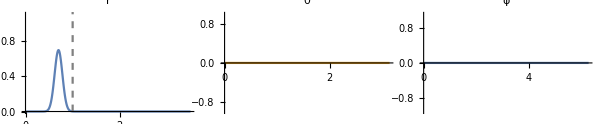

```mathematica
Show[Plot[fr[r],{r,0,3.5},PlotRange->{0,1.1},(*Ticks->None,*)PlotLabel->"r"],ListPlot[{{Rs,0},{Rs,10}},Joined->True,PlotStyle->{Dashed,Gray}]];
Plot[{fθ,D[fθ, θ]/fθm}//Evaluate,{θ,0,π},PlotRange->All,(*Ticks->None,*)PlotLabel->"θ"];
Plot[{D[fϕ, ϕ]/fϕm,fϕ}//Evaluate,{ϕ,0,2π},PlotRange->{-1.1,1.1},(*Ticks->None,*)PlotLabel->"ϕ"];
GraphicsRow[{%%%,%%,%},-5,ImageSize->600]
```

```mathematica
A2[l_,ω_]=(I Rs ω)/c2 ((1-α)SphericalBesselJ[l,(Rs ω)/c1] ((Rs ω)/ c2 SphericalHankelH2[l-1,(Rs ω)/c2]-(l+2) SphericalHankelH2[l,(Rs ω)/c2])-(1+α) SphericalHankelH2[l,(Rs ω)/c2]((Rs ω)/ c2 SphericalBesselJ[l-1,(Rs ω)/c1]- c1/c2 (l+2)SphericalBesselJ[l,(Rs ω)/c1]));

A1[l_,ω_]=-((I Rs ω)/c2) ((1-α)SphericalBesselJ[l,(Rs ω)/c1]( (Rs ω)/ c2 SphericalHankelH1[l-1,(Rs ω)/c2]-(l+2) SphericalHankelH1[l,(Rs ω)/c2])-(1+α)SphericalHankelH1[l,(Rs ω)/c2]( (Rs ω)/ c2 SphericalBesselJ[l-1,(Rs ω)/c1]-c1/c2 (l+2) SphericalBesselJ[l,(Rs ω)/c1]));

A21[l_,ω_]=( Rs ω )/(2 c2) I (1-α) SphericalHankelH2[l,(Rs ω)/c1](( Rs ω )/c2 SphericalHankelH2[l-1,(Rs ω)/c2]-(l+2) SphericalHankelH2[l,(Rs ω)/c2]) -(Rs ω)/(2c2) I(1+α) SphericalHankelH2[l,(Rs ω)/c2]  (( Rs ω )/c2 SphericalHankelH2[l-1,(Rs ω)/c1]- c1/c2 (l+2)SphericalHankelH2[l,(Rs ω)/c1]);
A22[l_,ω_]=( Rs ω )/(2 c2) I (1-α)SphericalHankelH1[l,(Rs ω)/c1] (( Rs ω )/c2 SphericalHankelH2[l-1,(Rs ω)/c2]-(l+2)SphericalHankelH2[l,(Rs ω)/c2])-( Rs ω  )/(2 c2) I (1+α) SphericalHankelH2[l,(Rs ω)/c2] (( Rs ω )/c2 SphericalHankelH1[l-1,(Rs ω)/c1]- c1/c2 (l+2) SphericalHankelH1[l,(Rs ω)/c1]) ;
A12[l_,ω_]=( Rs ω )/(2 c2) I (1-α) SphericalHankelH1[l,(Rs ω)/c1](-(( Rs ω )/c2) SphericalHankelH1[l-1,(Rs ω)/c2]-(l+2) SphericalHankelH1[l,(Rs ω)/c2]) -(Rs ω)/(2c2) I(1+α) SphericalHankelH1[l,(Rs ω)/c2]  (-(( Rs ω )/c2)SphericalHankelH1[l-1,(Rs ω)/c1]- c1/c2 (l+2)SphericalHankelH1[l,(Rs ω)/c1]);
A11[l_,ω_]=( Rs ω )/(2 c2) I (1-α)SphericalHankelH2[l,(Rs ω)/c1] (-(( Rs ω )/c2)SphericalHankelH1[l-1,(Rs ω)/c2]-(l+2)SphericalHankelH1[l,(Rs ω)/c2])-( Rs ω  )/(2 c2) I (1+α) SphericalHankelH1[l,(Rs ω)/c2] (-(( Rs ω )/c2) SphericalHankelH2[l-1,(Rs ω)/c1]- c1/c2 (l+2) SphericalHankelH2[l,(Rs ω)/c1]) ;
```

```mathematica
dA2[l_,ω_]:=-(1/(2 c1 c2^3))I Rs^2 ω(c2 ((1+α) Rs ω SphericalBesselJ[-2+l,(Rs ω)/c1] SphericalHankelH2[l,(Rs ω)/c2]+SphericalBesselJ[1+l,(Rs ω)/c1] (-(-1+α) Rs ω SphericalHankelH2[-1+l,(Rs ω)/c2]+((1+α) c1+(-1+α) c2) (2+l) SphericalHankelH2[l,(Rs ω)/c2]))-SphericalBesselJ[l,(Rs ω)/c1] (-(-1+α) c1 Rs ω SphericalHankelH2[-2+l,(Rs ω)/c2]+c1 ((-1+α) c2 l+(1+α) c1 (2+l)) SphericalHankelH2[-1+l,(Rs ω)/c2]-c1 Rs ω SphericalHankelH2[l,(Rs ω)/c2]+α c1 Rs ω SphericalHankelH2[l,(Rs ω)/c2]+c2 Rs ω SphericalHankelH2[l,(Rs ω)/c2]+α c2 Rs ω SphericalHankelH2[l,(Rs ω)/c2]-2 c1^2 SphericalHankelH2[1+l,(Rs ω)/c2]-2 α c1^2 SphericalHankelH2[1+l,(Rs ω)/c2]+2 c1 c2 SphericalHankelH2[1+l,(Rs ω)/c2]-2 α c1 c2 SphericalHankelH2[1+l,(Rs ω)/c2]-c1^2 l SphericalHankelH2[1+l,(Rs ω)/c2]-α c1^2 l SphericalHankelH2[1+l,(Rs ω)/c2]+c1 c2 l SphericalHankelH2[1+l,(Rs ω)/c2]-α c1 c2 l SphericalHankelH2[1+l,(Rs ω)/c2])+SphericalBesselJ[-1+l,(Rs ω)/c1] (((1+α) c1+(-1+α) c2) Rs ω SphericalHankelH2[-1+l,(Rs ω)/c2]-c2 ((1+α) c1 l+(-1+α) c2 (2+l)) SphericalHankelH2[l,(Rs ω)/c2]-(1+α) c1 Rs ω SphericalHankelH2[1+l,(Rs ω)/c2]));
```

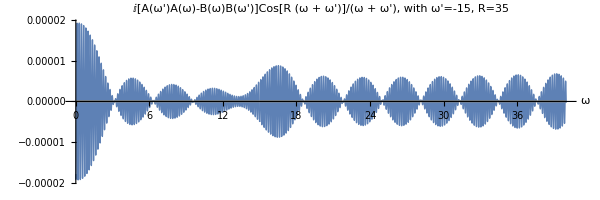

```mathematica
Plot[ReIm[ⅈ(A2[l,ωp]A2[l,ω]-A1[l,ω]A1[l,ωp])Cos[R(ω+ωp)]/(ω+ωp)]/.{l->1,ωp->-15,R->35}//Evaluate,{ω,0,40},PlotRange->All,ImageSize->600,AspectRatio->1/3,PlotPoints->400,PlotLabel->"ⅈ[A(ω')A(ω)-B(ω)B(ω')]Cos[R (ω + ω')]/(ω + ω'), with ω'=-15, R=35",AxesLabel->{"ω",},PlotStyle->Thin]
```

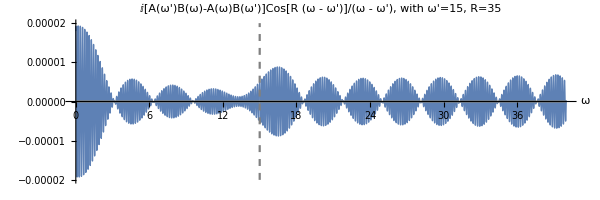

```mathematica
Show[Plot[ReIm[ⅈ(A2[l,ωp]A1[l,ω]-A2[l,ω]A1[l,ωp])Cos[R(ω-ωp)]/(ω-ωp)]/.{l->1,ωp->15,R->35}//Evaluate,{ω,0,40},PlotRange->All,ImageSize->600,AspectRatio->1/3,PlotPoints->400,PlotLabel->"ⅈ[A(ω')B(ω)-A(ω)B(ω')]Cos[R (ω - ω')]/(ω - ω'), with ω'=15, R=35",AxesLabel->{"ω",},PlotStyle->Thin],
ListLinePlot[{{15,-.00002},{15,.00002}},PlotStyle->{Dashed,Gray}]]
```

```mathematica
ab[l_,ω_]:=(mu1/c1^2)NIntegrate[Global`fr[r](1-α)SphericalBesselJ[l,(r ω)/c1]r^2,{r,0,Rs},WorkingPrecision->prec,MaxRecursion->maxrec,AccuracyGoal->accgl,PrecisionGoal->precgl]+(mu2/c2^2)NIntegrate[Global`fr[r] ((*A2[l,ω]SphericalHankelH1[l,(r ω)/c2]+*)A1[l,ω]SphericalHankelH2[l,(r ω)/c2])(*/2*) r^2,{r,Rs,5`64},WorkingPrecision->prec,MaxRecursion->maxrec,AccuracyGoal->accgl,PrecisionGoal->precgl];
```

```mathematica
Timing[
(*abe[n_,l_]:=ab[l,ww[n,l]];*)
Do[
abe[0,l]=Evaluate[ab[l,ww[0,l]]],
{l,1,lmax,2}];
Do[
abe[n,l]=Evaluate[ab[l,ww[n,l]]],
{n,1,nmax},{l,lmin,lmax}];]
```

NIntegrate::precw: The precision of the argument function ((3.36398523303962398496416954973×10^-26-8.40699686211609642420861940567186239605257203×10^-11 ⅈ) ⅇ^(-72 (-1739/2520+r)^2) r^3 SphericalHankelH2[4,(0.06987832154687253521552956767359432727794491442446755131377596447+5.153491698897748587144547935523653268422269897145600398374637548×10^-18 ⅈ) r]) is less than WorkingPrecision (47.8638).

NIntegrate::precw: The precision of the argument function ((1.5808219119509569707337×10^-31-1.41150913256043790843135367534552444399668×10^-12 ⅈ) ⅇ^(-72 (-1739/2520+r)^2) r^3 SphericalHankelH2[5,(0.08182470521515078882905649659862871013795504695223763954642777668+1.505570895511401815258653003053293646190107991778976705916241618×10^-21 ⅈ) r]) is less than WorkingPrecision (47.8638).

NIntegrate::precw: The precision of the argument function ((6.91038214142065×10^-37-2.3087975821121219413779319884987018163×10^-14 ⅈ) ⅇ^(-72 (-1739/2520+r)^2) r^3 SphericalHankelH2[6,(0.09355727046817058287211636335470702494052698015458993926292593836+4.158908484551324053044852126638229237352721391899979964890532548×10^-25 ⅈ) r]) is less than WorkingPrecision (47.8638).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

{51.4688,Null}

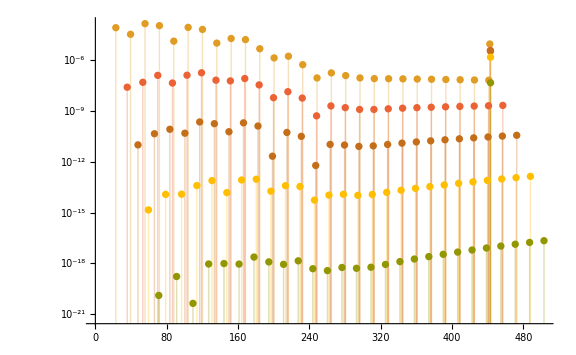

```mathematica
ListLogPlot[Table[{.77(2π 2.4 .01)^-1 Re[ww[n,l]],Global`thph[[l]]Abs[ (*ww[n,l]^2*)abe[n,l]/dA2[l,ww[n,l]]]},{l,1,10},{n,0,28}],ImageSize->Large,Filling->Axis(*,PlotRange->{{0,600},{-.0003,.001}}*)]
```

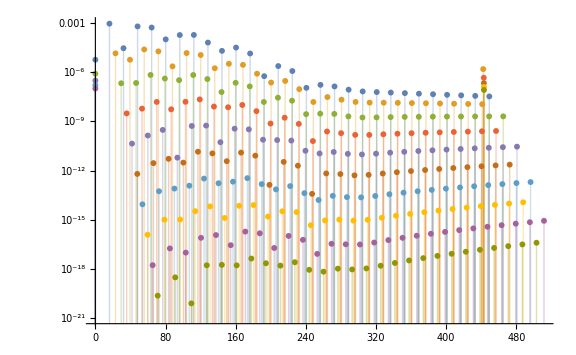

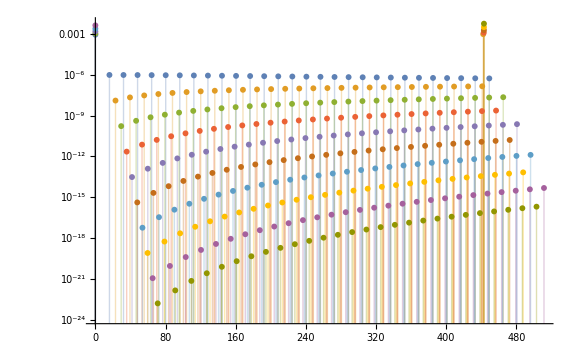

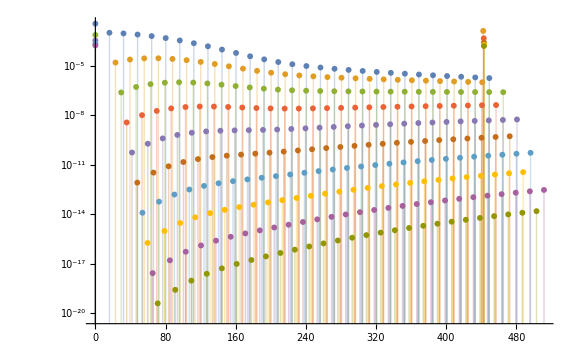

```mathematica
ListPlot[Table[{.77(2π 2.4 .01)^-1 Re[ww[n,l]],Abs[.5 A1[l,ww[n,l]]/(1-α)]^2/(.01Im[ww[n,l]])},{l,1,25},{n,1,40}],ImageSize->Large,PlotRange->{{0,400},{0,1.01}},GridLines->{{},{1}}]
```

-Graphics-

```mathematica
Do[
(* Account for the purely imaginary poles that occur for odd l; set even residues to zero*)
If[OddQ[lli]==True,
a0[0,lli]=2 I π ww[0,lli]^2abe[0,lli]/(2π c2 mu2 A1[lli,SetPrecision[ww[0,lli],164]] dA2[lli,SetPrecision[ww[0,lli],164]] lli(lli+1));
a1[0,lli]=(1-α)a0[0,lli];
a21[0,lli]=a0[0,lli]A21[lli,ww[0,lli]];
a22[0,lli]=a0[0,lli]A22[lli,ww[0,lli]];
a12[0,lli]=a0[0,lli]A12[lli,ww[0,lli]];
a11[0,lli]=a0[0,lli]A11[lli,ww[0,lli]];
,
a1[0,lli]=0;
a21[0,lli]=0;
a22[0,lli]=0;
a12[0,lli]=0;
a11[0,lli]=0;
];
(* Account for the poles that are symmetric about imaginary axis *)
Do[
ww[-nni,lli]=-Conjugate[ww[nni,lli]];
a0[nni,lli]=2 I π ww[nni,lli]^2abe[nni,lli]/(2π c2 mu2 A1[lli,SetPrecision[ww[nni,lli],164]] dA2[lli,SetPrecision[ww[nni,lli],164]] lli(lli+1));

a1[nni,lli]=(1-α)a0[nni,lli];
a1[-nni,lli]=(-1)^lli Conjugate[a1[nni,lli]];

a21[nni,lli]=a0[nni,lli]A21[lli,ww[nni,lli]];
a21[-nni,lli]=(-1)^lli Conjugate[a21[nni,lli]];

a22[nni,lli]=a0[nni,lli]A22[lli,ww[nni,lli]];
a22[-nni,lli]=(-1)^lli Conjugate[a22[nni,lli]];

a12[nni,lli]=a0[nni,lli]A12[lli,ww[nni,lli]];
a12[-nni,lli]=(-1)^lli Conjugate[a12[nni,lli]];

a11[nni,lli]=a0[nni,lli]A11[lli,ww[nni,lli]];
a11[-nni,lli]=(-1)^lli Conjugate[a11[nni,lli]];
,
{nni,1,nmax}];

,{lli,lmin,lmax}];//Timing
```

{2.32813,Null}

```mathematica
nmax
```

20

```mathematica
F2DC[nn_,lli_][rr_]:=(a12[nn,lli]+a11[nn,lli])SphericalHankelH2[lli,(rr ww[nn,lli])/c2];
```

```mathematica
f2DC=Table[F2DC[n,l][1.`48],{l,1,10},{n,1,20}];
```

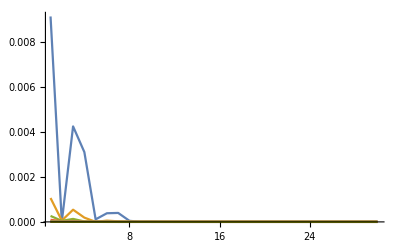

```mathematica
ListLinePlot[Re[f2DC],PlotRange->All]
```

```mathematica
Drop[Range[-nmax,nmax],{nmax+1}]
```

```mathematica
F1[nmax_,lli_][rr_,tt_]:=Sum[a1[nn,lli](SphericalHankelH1[lli,(rr ww[nn,lli])/c1]((1-UnitStep[-(rr/c1+tt)])Exp[I ww[nn,lli]tt]+(1-UnitStep[-(rr/c1-tt)])Exp[-I ww[nn,lli]tt])+SphericalHankelH2[lli,(rr ww[nn,lli])/c1]((1-UnitStep[-(-(rr/c1)+tt)])Exp[I ww[nn,lli]tt]+(1-UnitStep[-(-(rr/c1)-tt)])Exp[-I ww[nn,lli]tt])),{nn,-nmax,nmax}];
F2[nmax_,lli_][rr_,tt_]:=Sum[
a21[nn,lli]SphericalHankelH1[lli,(rr ww[nn,lli])/c2]((1-UnitStep[-(rr/c2-Rs/c1-Rs/c2+tt)])Exp[I ww[nn,lli]tt]+(1-UnitStep[-(rr/c2-Rs/c1-Rs/c2-tt)])Exp[-I ww[nn,lli]tt])+a22[nn,lli]SphericalHankelH1[lli,(rr ww[nn,lli])/c2]((1-UnitStep[-(rr/c2+Rs/c1-Rs/c2+tt)])Exp[I ww[nn,lli]tt]+(1-UnitStep[-(rr/c2+Rs/c1-Rs/c2-tt)])Exp[-I ww[nn,lli]tt])+a12[nn,lli]SphericalHankelH2[lli,(rr ww[nn,lli])/c2]((1-UnitStep[-(-(rr/c2)+Rs/c1+Rs/c2+tt)])Exp[I ww[nn,lli]tt]+(1-UnitStep[-(-(rr/c2)+Rs/c1+Rs/c2-tt)])Exp[-I ww[nn,lli]tt])+a11[nn,lli]SphericalHankelH2[lli,(rr ww[nn,lli])/c2]((1-UnitStep[-(-(rr/c2)-Rs/c1+Rs/c2+tt)])Exp[I ww[nn,lli]tt]+(1-UnitStep[-(-(rr/c2)-Rs/c1+Rs/c2-tt)])Exp[-I ww[nn,lli]tt]),
{nn,-nmax,nmax}];
```

```mathematica
F1t[nmax_,l_][r_,t_]:=2Sum[a1[n,l]SphericalBesselJ[l,(r ww[n,l])/c1]Exp[I ww[n,l]t],{n,-nmax,nmax}];
F2t[nmax_,l_][r_,t_]:=Sum[(a11[n,l]+a12[n,l])SphericalHankelH2[l,(r ww[n,l])/c2]Exp[I ww[n,l]t],{n,-nmax,nmax}];
```

```mathematica
lmin
lmax
```

1

10

```mathematica
f1b=Table[{r,F1t[20,l][r,t]},{l,lmin,lmax},{r,0,1,.02`48},{t,{2.6`48}(*0,.5`48,.02`48*)}];//Timing
```

{9.3125,Null}

```mathematica
f2b=Table[{r,F2t[20,l][r,t]},{l,lmin,lmax},{r,1,250,.25`48},{t,{2.6`48}(*0,.5`48,.02`48*)}];//Timing
```

{119.422,Null}

```mathematica
Dimensions[f1]
Dimensions[f2]
```

{10,51,16,2}

{10,513,16,2}

```mathematica
Manipulate[ListLogPlot[Join[(Sum[f1b[[l,;;,T,2]],{l,10}])^2,(Sum[f2b[[l,2;;,T,2]],{l,10}])^2],PlotRange->{1*^-24,1},Joined->True,AspectRatio->1/6,ImageSize->1000],{T,1,1,1}]
```

```mathematica
Do[
LLT=Transpose[{Join[Table[r,{r,0,1,.02}],Table[r,{r,1,250,.25}][[2;;]]],
Join[(Sum[f1b[[l,;;,T,2]],{l,10}])^2,(Sum[f2b[[l,2;;,T,2]],{l,10}])^2]}];
LLMov[T]=Show[ListLogLogPlot[LLT,PlotRange->{1*^-16,1},Joined->True,AspectRatio->1/4,ImageSize->1000,Frame->True,FrameLabel->{"r/R_*","amplitude^2"},PlotLabel->"t="<>ToString[2.6+(T-1).02]],
ListLogLogPlot[{{1,1},{1,1*^-10}},Joined->True,PlotStyle->{Dashed,Gray}]];,
{T,1,1,1}];
```

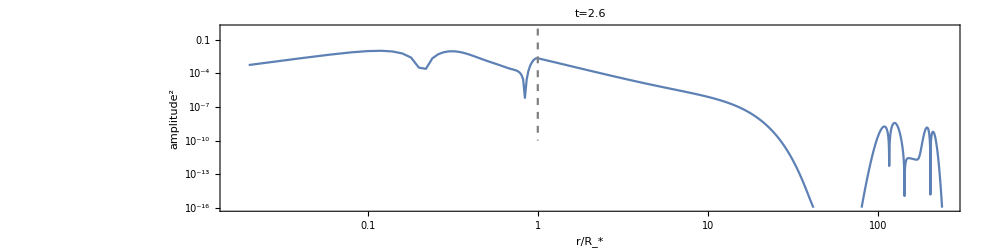

```mathematica
LLMov[1]
```

```mathematica
40000 4 4 36 4 10^-9 10^4/36^2/16.
```

0.0444444

```mathematica
InMovSnap=Table[ListLinePlot[Join[Sum[f1[[l,;;,T]],{l,10}],Sum[f2[[l,2;;,T]],{l,10}]],PlotRange->{-.2,.5},AspectRatio->1/6,ImageSize->1000],{T,1,7,1}];
```

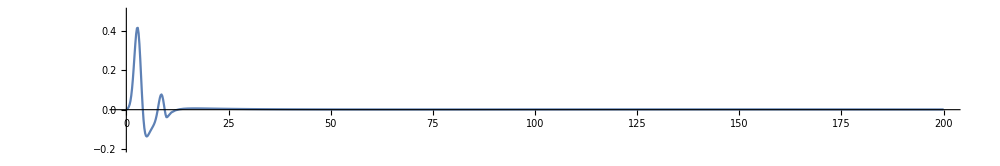

```mathematica
InMovSnap[[4]]
```

```mathematica
SetDirectory["C:\\Users\\joebr\\Documents\\QPO Research\\Mathematica Code\\Movies"]
```

C:\Users\joebr\Documents\QPO Research\Mathematica Code\Movies

```mathematica
Export["c100InLLR100.gif",LLMov/@Range[16],"DisplayDurations"->{.5},ImageResolution->100]
```

c100InLLR100.gif

```mathematica
Manipulate[ListLinePlot[(*Transpose[*)Sum[Re[f2[[l,;;,T]]],{l,10}](*,{2,1,3}]*),PlotRange->{-.3,1.25}],{T,1,13,1}]
```

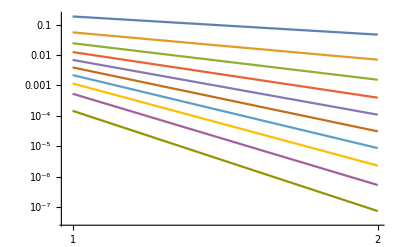

```mathematica
ListLogLogPlot[f2[[;;,;;,13,;;]],PlotRange->All,Joined->True]
```

```mathematica
Table[Sum[2000 Re[abe[n,l]],{n,1,20}],{l,1,10}]
```

{1.0836384270848192258688565765795527675455467328,0.80831858604040928001412469161073109899307185898,0.66813640198365398857511636601207315590555015394,0.58068715721267358695959041462710340829174976228,0.51976314085163930770317009284304038599929860643,0.47427401154732598067711412090874103000172916019,0.43866600369382211205990418693017814596104466328,0.40982489621684292877753254773824116703629893544,0.38585572841907262467831215103021861183744366291,0.36553181858717136137367136301082987472042666299}

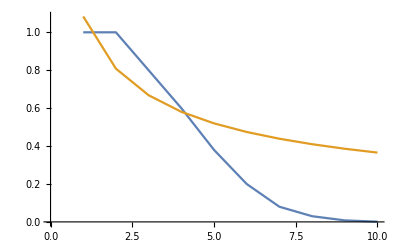

```mathematica
ListLinePlot[{amp,%378}]
```

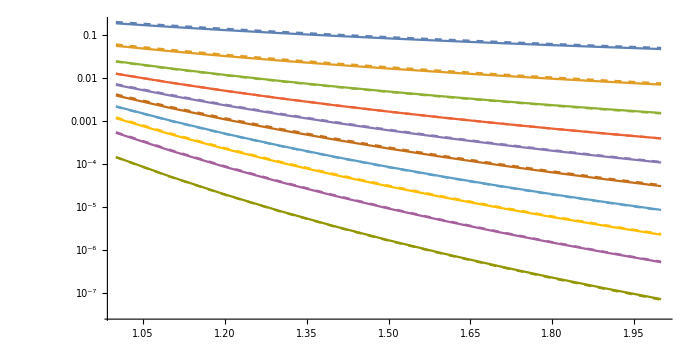

```mathematica
amp={1,1,.8,.6,.38,.2,.08,.03,.008,.0011};
Show[ListLogPlot[f2[[;;,;;,13,;;]],PlotRange->All,ImageSize->700,AspectRatio->1/2,Joined->True],
ListLogPlot[Table[{r,20 (.001)^(l+1)amp[[l]]((2l-1)!!)/(r/100)^(l+1)},{l,1,10},{r,1,2,.1}],PlotRange->All,ImageSize->700,AspectRatio->1/2,Joined->True,PlotStyle->Dashed]]
```

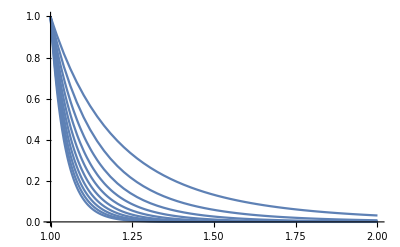

```mathematica
Plot[r^(-2#-3)&/@Range[10],{r,1,2},PlotRange->All]
```

```mathematica
Series[ⅈ SphericalHankelH1[1,z-ⅈ η],{η,0,2}]
```

```mathematica
ⅈ SphericalHankelH1[1,z]+(η (z SphericalHankelH1[0,z]-SphericalHankelH1[1,z]-z SphericalHankelH1[2,z]))/(2 z)
```

```mathematica
Show[%134,Plot[{4.3Exp[-Im[ww[1,2]]t],.05Exp[-Im[ww[2,2]]t],.009Exp[-Im[ww[3,2]]t],.016Exp[-Im[ww[4,2]]t],.0067Exp[-Im[ww[5,2]]t]},{t,0,200},PlotRange->{-.05,.1}]]
```

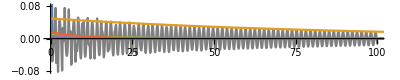

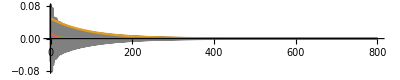

```mathematica
Exp[-Im[ww[2,2]]800]
```

0.00019590344073441394767327231506247079542630455119

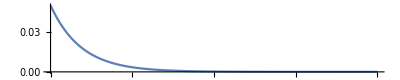

```mathematica
Plot[.05Exp[-Im[ww[2,2]]t],{t,0,1000},PlotRange->{0,.05},ImageSize->Full,AspectRatio->1/5]
```

```mathematica
f2//Dimensions
```

{1,5001,2}

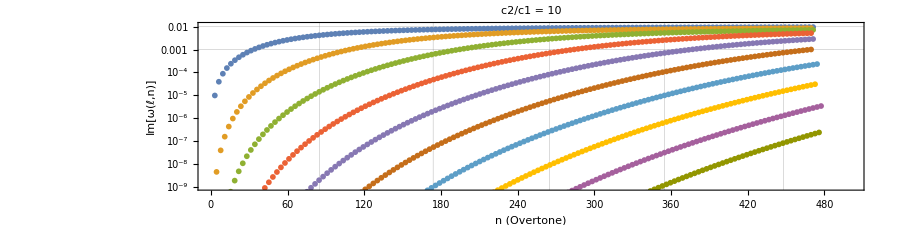

```mathematica
ListLogPlot[Table[ReIm[ww[n,l]],{l,10},{n,1,150}],GridLines->{{85,174,265,355,448},{.01,.001}},PlotRange->{{0,501},{0.000000001,.011}},AspectRatio->1/4,ImageSize->900,Frame->True,FrameLabel->{"n (Overtone)","Im[ω(ℓ,n)]"},PlotLabel->"c2/c1 = 10"]
```

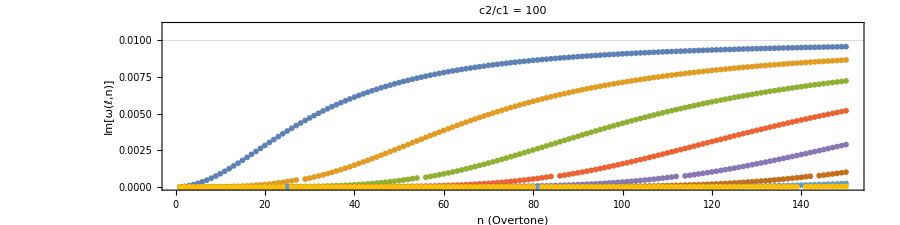

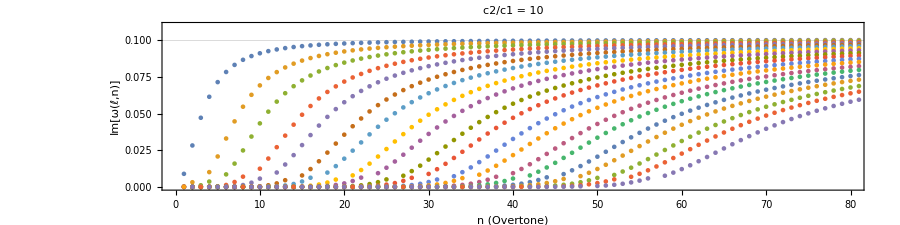

```mathematica
ww[4,1]
ww[1,2]
```

12.56513350777368658796785117579614611734646907893519238408025282+0.0001554441746506495477785031842732490134290873101735605572024020284 ⅈ

4.49325957193181575185024298565177044542938218483024218575886253+4.526417251174978958486629783217866471402286828865752639837245239×10^-9 ⅈ

```mathematica
c1=.
c2=.
Rs=.
α=.
```

```mathematica
(I Rs ω)/c2 ((1-α) SphericalBesselJ[l,(Rs ω)/c1] ((Rs ω)/ c2 SphericalHankelH2[l-1,(Rs ω)/c2]-(l+2) SphericalHankelH2[l,(Rs ω)/c2])-(1+α) SphericalHankelH2[l,(Rs ω)/c2]((Rs ω)/ c2 SphericalBesselJ[l-1,(Rs ω)/c1]- c1/c2 (l+2) SphericalBesselJ[l,(Rs ω)/c1]))/.α->(μ1 c2-μ2 c1)/(μ1 c2+μ2 c1)/.{l->1(*,Rs->1,c1->1*)}//FunctionExpand//FullSimplify
```

(2 c1 ⅇ^(-(ⅈ Rs ω)/c2) (c1 Rs ω (3 c2^2 (μ1-μ2)+3 ⅈ c2 Rs (μ1-μ2) ω+Rs^2 μ2 ω^2) Cos[(Rs ω)/c1]+(c2 Rs^2 μ1 ω^2 (c2+ⅈ Rs ω)-c1^2 (3 c2^2 (μ1-μ2)+3 ⅈ c2 Rs (μ1-μ2) ω+Rs^2 μ2 ω^2)) Sin[(Rs ω)/c1]))/(c2 Rs^3 (c2 μ1+c1 μ2) ω^3)

```mathematica
(c1 Rs ω (3 c2^2 (μ1-μ2)+3 ⅈ c2 Rs (μ1-μ2) ω+Rs^2 μ2 ω^2) Cos[(Rs ω)/c1]+(c2 Rs^2 μ1 ω^2 (c2+ⅈ Rs ω)-c1^2 (3 c2^2 (μ1-μ2)+3 ⅈ c2 Rs (μ1-μ2) ω+Rs^2 μ2 ω^2)) Sin[(Rs ω)/c1])
```

```mathematica
c2 Rs^2 μ1 ω^2 (c2+ⅈ Rs ω)-c1^2 (3 c2^2 (μ1-μ2)+3 ⅈ c2 Rs (μ1-μ2) ω+Rs^2 μ2 ω^2)//Expand
```

-3 c1^2 c2^2 μ1+3 c1^2 c2^2 μ2-3 ⅈ c1^2 c2 Rs μ1 ω+3 ⅈ c1^2 c2 Rs μ2 ω+c2^2 Rs^2 μ1 ω^2-c1^2 Rs^2 μ2 ω^2+ⅈ c2 Rs^3 μ1 ω^3

```mathematica
(I Rs ω)/c2 ((1-α) SphericalBesselJ[l,(Rs ω)/c1] (a(Rs ω)/ c2 SphericalHankelH2[l-1,(Rs ω)/c2]-c(l+2) SphericalHankelH2[l,(Rs ω)/c2])-(1+α) SphericalHankelH2[l,(Rs ω)/c2](b(Rs ω)/ c2 SphericalBesselJ[l-1,(Rs ω)/c1]- c1/c2 d(l+2) SphericalBesselJ[l,(Rs ω)/c1]))/.α->(c2-c1)/(c2+c1)/.{l->1,Rs->1,c1->1}//FunctionExpand//FullSimplify
```

(ⅇ^(-(ⅈ ω)/c2) (2 ω (3 c2^2 (-c+d)-3 ⅈ c2 (c-d) ω+a ω^2) Cos[ω]+2 (3 c2^2 (c-d)+3 ⅈ c2 (c-d) ω+(-a+b c2^2) ω^2+ⅈ b c2 ω^3) Sin[ω]))/(c2 (1+c2) ω^3)

```mathematica
D[SphericalBesselJ[1,r ω/c1],r]-SphericalBesselJ[1,r ω/c1]/r/.r->Rs//FunctionExpand
```

(3 c1 Rs ω Cos[(Rs ω)/c1]+(-3 c1^2+Rs^2 ω^2) Sin[(Rs ω)/c1])/(Rs^3 ω^2)

```mathematica
FindRoot[ω Cos[ω]-Sin[ω]==0,{ω,4.14+ⅈ}]
```

{ω→4.49341-4.62223×10^-32 ⅈ}

```mathematica
FindRoot[(6 c2 ω-6 c2^3 ω+6 ⅈ ω^2-6 ⅈ c2^2 ω^2+2 c2 ω^3) Cos[ω]-(-6 c2+6 c2^3-6 ⅈ ω+6 ⅈ c2^2 ω+2 ⅈ ω^3) Sin[ω]==0/.c2->3,{ω,5}]
```

{ω→5.09497-0.113749 ⅈ}

```mathematica
FindRoot[ω Cos[ω]+(-1+c2^2+ⅈ c2 ω) Sin[ω]==0/.c2->100,{ω,3.1}]
```

{ω→3.14128+9.85889×10^-6 ⅈ}

```mathematica
Re[ww[1,1]]
```

3.141278803999049143849296823181390171953081760708143024681593697

```mathematica
ω Cos[ω]+(-1+c2^2+ⅈ c2 ω) Sin[ω]/.{c2->100,ω->Re[ww[1,1]]}
```

-0.0030966429577156598173104227465438221713648897001510793139+0.098588905086293121393236030313746829897837204293327018389088 ⅈ

```mathematica
z Cos[z]/.z->z+ⅈ α
%//TrigExpand
%//TrigToExp
Series[%%,{α,0,3}]
```

(z+ⅈ α) Cos[z+ⅈ α]

z Cos[z] Cosh[α]+ⅈ α Cos[z] Cosh[α]-ⅈ z Sin[z] Sinh[α]+α Sin[z] Sinh[α]

1/2 ⅇ^(ⅈ z-α) z+1/2 ⅇ^(-ⅈ z+α) z+1/2 ⅈ ⅇ^(ⅈ z-α) α+1/2 ⅈ ⅇ^(-ⅈ z+α) α

z Cos[z]+ⅈ (Cos[z]-z Sin[z]) α+(1/2 z Cos[z]+Sin[z]) α^2+1/6 ⅈ (3 Cos[z]-z Sin[z]) α^3+O[α]^4

```mathematica
(1-c21^2-ⅈ c21 z) Sin[z]/.z->z+ⅈ α
%//TrigExpand
%//TrigToExp
Series[%%,{α,0,3}]//Simplify
```

(1-c21^2-ⅈ c21 (z+ⅈ α)) Sin[z+ⅈ α]

Cosh[α] Sin[z]-c21^2 Cosh[α] Sin[z]-ⅈ c21 z Cosh[α] Sin[z]+c21 α Cosh[α] Sin[z]+ⅈ Cos[z] Sinh[α]-ⅈ c21^2 Cos[z] Sinh[α]+c21 z Cos[z] Sinh[α]+ⅈ c21 α Cos[z] Sinh[α]

-1/2 ⅈ ⅇ^(ⅈ z-α)+1/2 ⅈ c21^2 ⅇ^(ⅈ z-α)+1/2 ⅈ ⅇ^(-ⅈ z+α)-1/2 ⅈ c21^2 ⅇ^(-ⅈ z+α)-1/2 c21 ⅇ^(ⅈ z-α) z+1/2 c21 ⅇ^(-ⅈ z+α) z-1/2 ⅈ c21 ⅇ^(ⅈ z-α) α+1/2 ⅈ c21 ⅇ^(-ⅈ z+α) α

-(-1+c21^2+ⅈ c21 z) Sin[z]+((ⅈ-ⅈ c21^2+c21 z) Cos[z]+c21 Sin[z]) α+1/2 (2 ⅈ c21 Cos[z]-(-1+c21^2+ⅈ c21 z) Sin[z]) α^2+1/6 ((ⅈ-ⅈ c21^2+c21 z) Cos[z]+3 c21 Sin[z]) α^3+O[α]^4

```mathematica
FindRoot[D[Log[SphericalBesselJ[1,z]],z]==D[Log[SphericalHankelH1[1,z/100]],z],{z,3.1+.1ⅈ}]
```

(-SphericalBesselJ[1,z]/(2 z)+1/2 (SphericalBesselJ[0,z]-SphericalBesselJ[2,z]))/SphericalBesselJ[1,z]-(-(50 SphericalHankelH1[1,z/100])/z+1/2 (SphericalHankelH1[0,z/100]-SphericalHankelH1[2,z/100]))/(100 SphericalHankelH1[1,z/100])

```mathematica
Series[D[Log[SphericalBesselJ[3,z]],z],{z,0,10}]
```

3/z-z/9-z^3/891-(2 z^5)/104247-(19 z^7)/51602265-(58 z^9)/7895146545+O[z]^11

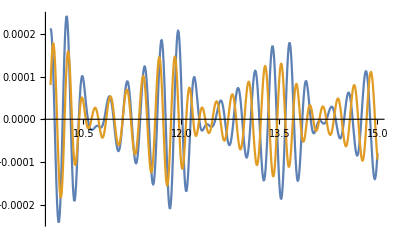

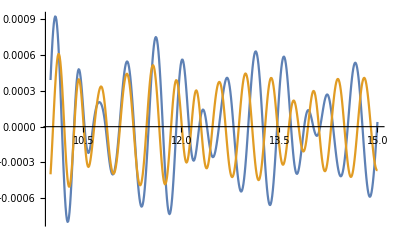

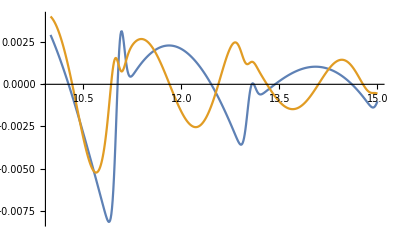

```mathematica
abi1[l_,n_,rp_]:=(mu1/c1^2)NIntegrate[fr(1-α)SphericalHankelH1[l,(r ww[n,l])/c1]/2 r^2,{r,rp,Rs},WorkingPrecision->prec,MaxRecursion->maxrec,AccuracyGoal->accgl,PrecisionGoal->precgl];
abi2[l_,n_,rp_]:=(mu1/c1^2)NIntegrate[fr(1-α)SphericalHankelH2[l,(r ww[n,l])/c1]/2 r^2,{r,0,rp},WorkingPrecision->prec,MaxRecursion->maxrec,AccuracyGoal->accgl,PrecisionGoal->precgl];

abo1[l_,n_,rp_]:=(mu2/c2^2)NIntegrate[fr (SphericalHankelH1[l,(r ww[n,l])/c2])/2 r^2,{r,rp,rmax},WorkingPrecision->prec,MaxRecursion->maxrec,AccuracyGoal->accgl,PrecisionGoal->precgl];
abo2[l_,n_,rp_]:=(mu2/c2^2)NIntegrate[fr (SphericalHankelH2[l,(r ww[n,l])/c2])/2 r^2,{r,Rs,rp},WorkingPrecision->prec,MaxRecursion->maxrec,AccuracyGoal->accgl,PrecisionGoal->precgl];
```

```mathematica
Do[
(* Account for the purely imaginary poles that occur for odd l; set even residues to zero*)
If[OddQ[lli]==True,
a0[0,lli]=2 π I ww[0,lli]^2/(2π c2 mu2 lli(lli+1) A1[lli,SetPrecision[ww[0,lli],64]] dA2[lli,SetPrecision[ww[0,lli],64]]);
a1[0,lli]=a0[0,lli];
a21[0,lli]=a0[0,lli]A21[lli,SetPrecision[ww[0,lli],64]];
a22[0,lli]=a0[0,lli]A22[lli,SetPrecision[ww[0,lli],64]];
a12[0,lli]=a0[0,lli]A12[lli,SetPrecision[ww[0,lli],64]];
a11[0,lli]=a0[0,lli]A11[lli,SetPrecision[ww[0,lli],64]];
,
a1[0,lli]=0;
a21[0,lli]=0;
a22[0,lli]=0;
a12[0,lli]=0;
a11[0,lli]=0;
];
(* Account for the poles that are symmetric about imaginary axis *)
Do[
ww[-nni,lli]=-Conjugate[ww[nni,lli]];
a0[nni,lli]=2 π I  ww[nni,lli]^2/(2π c2 mu2 lli(lli+1) A1[lli,SetPrecision[ww[nni,lli],64]] dA2[lli,SetPrecision[ww[nni,lli],64]]);

a1[nni,lli]=a0[nni,lli];
a1[-nni,lli]=Conjugate[a1[nni,lli]];

a21[nni,lli]=a0[nni,lli]A21[lli,SetPrecision[ww[nni,lli],64]];
a21[-nni,lli]=Conjugate[a21[nni,lli]];

a22[nni,lli]=a0[nni,lli]A22[lli,SetPrecision[ww[nni,lli],64]];
a22[-nni,lli]=Conjugate[a22[nni,lli]];

a12[nni,lli]=a0[nni,lli]A12[lli,SetPrecision[ww[nni,lli],64]];
a12[-nni,lli]=Conjugate[a12[nni,lli]];

a11[nni,lli]=a0[nni,lli]A11[lli,SetPrecision[ww[nni,lli],64]];
a11[-nni,lli]=Conjugate[a11[nni,lli]];
,
{nni,1,nmax}];

,{lli,lmin,lmax}];//Timing
```

{1.28125,Null}

```mathematica
test[arg_]:=If[1>arg>0,1,0,2]
```

```mathematica
Θ[x_]:=Evaluate[(1-UnitStep[-x])];

abpi1[l_,n_,arg_]:=If[-Rs<arg<0,
abi1[l,n,-arg],

If[0<arg,
abi1[l,n,0],
0,
"error11"],

"error12"]

abpi2[l_,n_,arg_]:=If[0<arg<Rs,
abi2[l,n,arg],

If[Rs<arg,
abi2[l,n,Rs],
0,
"error21"],

"error22"]

abpo1[l_,n_,arg_]:=If[-rmax<arg<-Rs,
abo1[l,n,-arg],

If[Rs<arg,
abo1[l,n,0],
0,
"error11"],

"error12"]

abpo2[l_,n_,arg_]:=If[Rs<arg<rmax,
abo2[l,n,arg],

If[rmax<arg,
abo2[l,n,rmax],
0,
"error21"],

"error22"]
```

```mathematica
F1p[nmax_,l_][r_,t_]:=
(1-α)Sum[a1[n,l]((SphericalHankelH1[l, ww[n,l] r/c1](Θ[r/c1+Rs/c1(*rp/c1*)+t]abpi1[l,n,r/c1+t]Exp[I ww[n,l]t]+Θ[r/c1+Rs/c1(*rp/c1*)-t]abpi1[l,n,r/c1-t]Exp[-I ww[n,l]t])
+SphericalHankelH2[l,ww[n,l] r/c1](Θ[-r/c1+Rs/c1(*rp/c1*)+t]abpi1[l,n,-r/c1+t]Exp[I ww[n,l]t]+Θ[-r/c1+Rs/c1(*rp/c1*)-t]abpi1[l,n,-r/c1-t]Exp[-I ww[n,l]t]))
+(SphericalHankelH1[l, ww[n,l] r/c1](Θ[r/c1-0/c1(*rp/c1*)+t]abpi2[l,n,r/c1+t]Exp[I ww[n,l]t]+Θ[r/c1-0/c1(*rp/c1*)-t]abpi2[l,n,r/c1-t]Exp[-I ww[n,l]t])
+SphericalHankelH2[l,ww[n,l] r/c1](Θ[-r/c1-0/c1(*rp/c1*)+t]abpi2[l,n,-r/c1+t]Exp[I ww[n,l]t]+Θ[-r/c1-0/c1(*rp/c1*)-t]abpi2[l,n,-r/c1-t]Exp[-I ww[n,l]t])))
+((SphericalHankelH1[l, ww[n,l] r/c1](
Exp[I ww[n,l]t](a21[n,l]Θ[r/c1+rmax/c2(*rp/c2*)-Rs/c1-Rs/c2+t]abpo1[l,n,r/c1-Rs/c1-Rs/c2+t]+a22[n,l]Θ[r/c1+rmax/c2(*rp/c2*)+Rs/c1-Rs/c2+t]abpo1[l,n,r/c1+Rs/c1-Rs/c2+t])
+Exp[-I ww[n,l]t](a21[n,l]Θ[r/c1+rmax/c2(*rp/c2*)-Rs/c1-Rs/c2-t]abpo1[l,n,r/c1-Rs/c1-Rs/c2-t]+a22[n,l]Θ[r/c1+rmax/c2(*rp/c2*)+Rs/c1-Rs/c2-t]abpo1[l,n,r/c1+Rs/c1-Rs/c2-t]))
+SphericalHankelH2[l,ww[n,l] r/c1](
Exp[I ww[n,l]t](a21[n,l]Θ[-r/c1+rmax/c2(*rp/c2*)-Rs/c1-Rs/c2+t]abpo1[l,n,-r/c1-Rs/c1-Rs/c2+t]+a22[n,l]Θ[-r/c1+rmax/c2(*rp/c2*)+Rs/c1-Rs/c2+t]abpo1[l,n,-r/c1+Rs/c1-Rs/c2+t])
+Exp[-I ww[n,l]t](a21[n,l]Θ[-r/c1+rmax/c2(*rp/c2*)-Rs/c1-Rs/c2-t]abpo1[l,n,-r/c1-Rs/c1-Rs/c2-t]+a22[n,l]Θ[-r/c1+rmax/c2(*rp/c2*)+Rs/c1-Rs/c2-t]abpo1[l,n,-r/c1+Rs/c1-Rs/c2-t])))
+(SphericalHankelH1[l, ww[n,l] r/c1](
Exp[I ww[n,l]t](a12[n,l]Θ[r/c1-Rs/c2(*rp/c2*)+Rs/c1+Rs/c2+t]abpo2[l,n,r/c1+Rs/c1+Rs/c2+t]+a11[n,l]Θ[r/c1-Rs/c2(*rp/c2*)-Rs/c1+Rs/c2+t]abpo2[l,n,r/c1-Rs/c1+Rs/c2+t])
+Exp[-I ww[n,l]t](a12[n,l]Θ[r/c1-Rs/c2(*rp/c2*)+Rs/c1+Rs/c2-t]abpo2[l,n,r/c1+Rs/c1+Rs/c2-t]+a11[n,l]Θ[r/c1-Rs/c2(*rp/c2*)-Rs/c1+Rs/c2-t]abpo2[l,n,r/c1-Rs/c1+Rs/c2-t]))
+SphericalHankelH2[l,ww[n,l] r/c1](
Exp[I ww[n,l]t](a12[n,l]Θ[-r/c1-Rs/c2(*rp/c2*)+Rs/c1+Rs/c2+t]abpo2[l,n,-r/c1+Rs/c1+Rs/c2+t]+a11[n,l]Θ[-r/c1-Rs/c2(*rp/c2*)-Rs/c1+Rs/c2+t]abpo2[l,n,-r/c1-Rs/c1+Rs/c2+t])
+Exp[-I ww[n,l]t](a12[n,l]Θ[-r/c1-Rs/c2(*rp/c2*)+Rs/c1+Rs/c2-t]abpo2[l,n,-r/c1+Rs/c1+Rs/c2-t]+a11[n,l]Θ[-r/c1-Rs/c2(*rp/c2*)-Rs/c1+Rs/c2-t]abpo2[l,n,-r/c1-Rs/c1+Rs/c2-t])))),{n,-nmax,nmax}];
```

```mathematica
F2p[nmax_,l_][r_,t_]:=Sum[(SphericalHankelH1[l, ww[n,l] r/c2](Exp[I ww[n,l]t](a21[n,l]abpi1[l,n,r/c2-Rs/c1-Rs/c2+t]Θ[r/c2+Rs/c1(*rp/c1*)-Rs/c1-Rs/c2+t]+a22[n,l]abpi1[l,n,r/c2+Rs/c1-Rs/c2+t]Θ[r/c2+Rs/c1(*rp/c1*)+Rs/c1-Rs/c2+t])+Exp[-I ww[n,l]t](a21[n,l]abpi1[l,n,r/c2-Rs/c1-Rs/c2-t]Θ[r/c2+Rs/c1(*rp/c1*)-Rs/c1-Rs/c2-t]+a22[n,l]abpi1[l,n,r/c2+Rs/c1-Rs/c2-t]Θ[r/c2+Rs/c1(*rp/c1*)+Rs/c1-Rs/c2-t]))+SphericalHankelH2[l, ww[n,l] r/c2](Exp[I ww[n,l]t](a11[n,l]abpi1[l,n,-r/c2-Rs/c1+Rs/c2+t]Θ[-r/c2+Rs/c1(*rp/c1*)-Rs/c1+Rs/c2+t]+a12[n,l]abpi1[l,n,-r/c2+Rs/c1+Rs/c2+t]Θ[-r/c2+Rs/c1(*rp/c1*)+Rs/c1+Rs/c2+t])+Exp[-I ww[n,l]t](a11[n,l]abpi1[l,n,-r/c2-Rs/c1+Rs/c2-t]Θ[-r/c2+Rs/c1(*rp/c1*)-Rs/c1+Rs/c2-t]+a12[n,l]abpi1[l,n,-r/c2+Rs/c1+Rs/c2-t]Θ[-r/c2+Rs/c1(*rp/c1*)+Rs/c1+Rs/c2-t]))+SphericalHankelH1[l, ww[n,l] r/c2](Exp[I ww[n,l]t](a21[n,l]abpi2[l,n,r/c2-Rs/c1-Rs/c2+t]Θ[r/c2-0/c1(*rp/c1*)-Rs/c1-Rs/c2+t]+a22[n,l]abpi2[l,n,r/c2+Rs/c1-Rs/c2+t]Θ[r/c2-0/c1(*rp/c1*)+Rs/c1-Rs/c2+t])+Exp[-I ww[n,l]t](a21[n,l]abpi2[l,n,r/c2-Rs/c1-Rs/c2-t]Θ[r/c2-0/c1(*rp/c1*)-Rs/c1-Rs/c2-t]+a22[n,l]abpi2[l,n,r/c2+Rs/c1-Rs/c2-t]Θ[r/c2-0/c1(*rp/c1*)+Rs/c1-Rs/c2-t]))+SphericalHankelH2[l, ww[n,l] r/c2](Exp[I ww[n,l]t](a11[n,l]abpi2[l,n,-r/c2-Rs/c1+Rs/c2+t]Θ[-r/c2-0/c1(*rp/c1*)-Rs/c1+Rs/c2+t]+a12[n,l]abpi2[l,n,-r/c2+Rs/c1+Rs/c2+t]Θ[-r/c2-0/c1(*rp/c1*)+Rs/c1+Rs/c2+t])+Exp[-I ww[n,l]t](a11[n,l]abpi2[l,n,-r/c2-Rs/c1+Rs/c2-t]Θ[-r/c2-0/c1(*rp/c1*)-Rs/c1+Rs/c2-t]+a12[n,l]abpi2[l,n,-r/c2+Rs/c1+Rs/c2-t]Θ[-r/c2-0/c1(*rp/c1*)+Rs/c1+Rs/c2-t])))+(SphericalHankelH1[l, ww[n,l] r/c2](Exp[I ww[n,l]t](a21[n,l]^2 abpo1[l,n,r/c2-2 Rs/c1-2 Rs/c2+t]Θ[r/c2+rmax/c2(*rp/c2*)-2 Rs/c1-2 Rs/c2+t]+2 a21[n,l]a22[n,l]abpo1[l,n,r/c2-2 Rs/c2+t]Θ[r/c2+rmax/c2(*rp/c2*)-2 Rs/c2+t]+a22[n,l]^2 abpo1[l,n,r/c2+2 Rs/c1-2 Rs/c2+t]Θ[r/c2+rmax/c2(*rp/c2*)+2 Rs/c1-2 Rs/c2+t])+Exp[-I ww[n,l]t](a21[n,l]^2 abpo1[l,n,r/c2-2 Rs/c1-2 Rs/c2-t]Θ[r/c2+rmax/c2(*rp/c2*)-2 Rs/c1-2 Rs/c2-t]+2 a21[n,l]a22[n,l]abpo1[l,n,r/c2-2 Rs/c2-t]Θ[r/c2+rmax/c2(*rp/c2*)-2 Rs/c2-t]+a22[n,l]^2 abpo1[l,n,r/c2+2 Rs/c1-2 Rs/c2-t]Θ[r/c2+rmax/c2(*rp/c2*)+2 Rs/c1-2 Rs/c2-t]))+SphericalHankelH2[l, ww[n,l] r/c2](Exp[I ww[n,l]t](a11[n,l]a21[n,l]abpo1[l,n,-r/c2-2 Rs/c1+t]Θ[-r/c2+rmax/c2(*rp/c2*)-2 Rs/c1+t]+( a11[n,l]a22[n,l]+ a12[n,l]a21[n,l])abpo1[l,n,-r/c2+t]Θ[-r/c2+rmax/c2(*rp/c2*)+t]+ a12[n,l]a22[n,l]abpo1[l,n,-r/c2+2 Rs/c1+t]Θ[-r/c2+rmax/c2(*rp/c2*)+2 Rs/c1+t])+Exp[-I ww[n,l]t](a11[n,l]a21[n,l]abpo1[l,n,-r/c2-2 Rs/c1-t]Θ[-r/c2+rmax/c2(*rp/c2*)-2 Rs/c1-t]+( a11[n,l]a22[n,l]+ a12[n,l]a21[n,l])abpo1[l,n,-r/c2-t]Θ[-r/c2+rmax/c2(*rp/c2*)-t]+ a12[n,l]a22[n,l]abpo1[l,n,-r/c2+2 Rs/c1-t]Θ[-r/c2+rmax/c2(*rp/c2*)+2 Rs/c1-t]))+SphericalHankelH1[l, ww[n,l] r/c2](Exp[I ww[n,l]t](a11[n,l]a21[n,l]abpo2[l,n,r/c2-2 Rs/c1+t]Θ[r/c2-Rs/c2(*rp/c2*)-2 Rs/c1+t]+( a11[n,l]a22[n,l]+ a12[n,l]a21[n,l])abpo2[l,n,r/c2+t]Θ[r/c2-Rs/c2(*rp/c2*)+t]+ a12[n,l]a22[n,l]abpo2[l,n,r/c2+2 Rs/c1+t]Θ[r/c2-Rs/c2(*rp/c2*)+2 Rs/c1+t])+Exp[-I ww[n,l]t](a11[n,l]a21[n,l]abpo2[l,n,r/c2-2 Rs/c1-t]Θ[r/c2-Rs/c2(*rp/c2*)-2 Rs/c1-t]+( a11[n,l]a22[n,l]+ a12[n,l]a21[n,l])abpo2[l,n,r/c2-t]Θ[r/c2-Rs/c2(*rp/c2*)-t]+ a12[n,l]a22[n,l]abpo2[l,n,r/c2+2 Rs/c1-t]Θ[r/c2-Rs/c2(*rp/c2*)+2 Rs/c1-t]))+SphericalHankelH2[l, ww[n,l] r/c2](Exp[I ww[n,l]t](a12[n,l]^2 abpo2[l,n,-r/c2+2 Rs/c1+2 Rs/c2+t]Θ[-r/c2-Rs/c2(*rp/c2*)-2 Rs/c1+t]+2 a11[n,l]a12[n,l]abpo2[l,n,-r/c2+2 Rs/c2+t]Θ[-r/c2-Rs/c2(*rp/c2*)+2 Rs/c2+t]+ a11[n,l]^2 abpo2[l,n,-r/c2-2 Rs/c1+2 Rs/c2+t]Θ[-r/c2-Rs/c2(*rp/c2*)-2 Rs/c1+2 Rs/c2+t])+Exp[-I ww[n,l]t](a12[n,l]^2 abpo2[l,n,-r/c2+2 Rs/c1+2 Rs/c2-t]Θ[-r/c2-Rs/c2(*rp/c2*)-2 Rs/c1-t]+2 a11[n,l]a12[n,l]abpo2[l,n,-r/c2+2 Rs/c2-t]Θ[-r/c2-Rs/c2(*rp/c2*)+2 Rs/c2-t]+ a11[n,l]^2 abpo2[l,n,-r/c2-2 Rs/c1+2 Rs/c2-t]Θ[-r/c2-Rs/c2(*rp/c2*)-2 Rs/c1+2 Rs/c2-t]))),{n,-nmax,nmax}];
```

```mathematica
Table[{t,F2t[50,1][1.5`64,t]},{t,0,20,.01`64}];
```

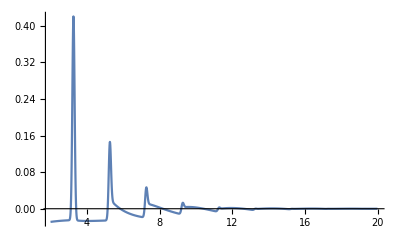

```mathematica
ListLinePlot[%213[[200;;2000]],PlotRange->All]
```

```mathematica
Timing[F2p[50,1][2.9`64,0]]
```

{155.344,15.458199576400891432414740745546375541263719024220068300946+0. ⅈ}

```mathematica
Table[{n,F2p[n,1][2.9`64,0]},{n,70,80,10}]
```

{{70,15.43736955050432400106826640476347538970654236290233930175+0. ⅈ},{80,15.469273389429220316787466124166933950671597871160236221459+0. ⅈ}}

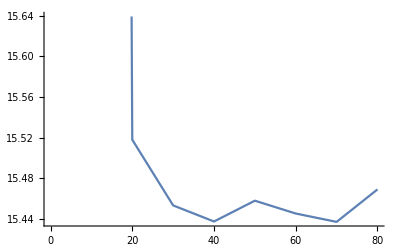

```mathematica
ListLinePlot[Join[%191,%193]]
```

```mathematica
Timing[F1p[50,1][.75`64,0.5`64]]
```

{105.469,0.48544829685240870729261786686537203128734916598128287933804+0. ⅈ}

```mathematica
ww[0,4]
```

ww[0,4]

```mathematica
SetDirectory["C:\\Users\\joebr\\OneDrive\\Documents\\QPO Research\\Mathematica Code\\Hyalite\\Contour\\Prime"];
FileNames[]
```

{c2PF1.m,c2PF2.m,c2P.m,F1pcC2ic0p5sr1o8Ri0p01Rb1time0p2s0p2l1.Mx,F1pcC2ic0p5sr1o8Ri0p01Rb1time0p2s0p2l1n70.Mx,F1pcC2ic0p5sr1o8Ri0p01Rb1time0p2s0p2l2.Mx,F1pcC2ic0p5sr1o8Ri0p01Rb1time0p2s0p2l2n70.Mx,F1pcC2ic1p5sr1o8Ri0p1Rb1time0p51s0p02l1n50.Mx,F1pcC2ic1p5sr1o8Ri0p1Rb1time0p51s0p02l2n50.Mx,F1pcC2ic1p5sr1o8Ri0p1Rb1time0p5s0p5l1n50.Mx,F1pcC2ic1p5sr1o8Ri0p1Rb1time0p5s0p5l1n70.Mx,F1pcC2ic1p5sr1o8Ri0p1Rb1time0p5s0p5l2n50.Mx,F1pcC2ic1p5sr1o8Ri0p1Rb1time0p5s0p5l2n70.Mx,F1pcC2ic3sr1o8Ri0p02Rb1time1p71l1n50.Mx,F1pcC2ic3sr1o8Ri0p02Rb1time1p71l1n70.Mx,F1pcC2ic3sr1o8Ri0p02Rb1time1p71l1n70SP.Mx,F1pcC2ic3sr1o8Ri0p02Rb1time1p71l2n50.Mx,F1pcC2ic3sr1o8Ri0p02Rb1time1p71l2n70.Mx,F1pcC2ic3sr1o8Ri0p02Rb1time1p71l2n70SP.Mx,F2pcC2ic3sr1o8Ri1p02Rb4time0l1n50.Mx,F2pcC2ic3sr1o8Ri1p02Rb4time0l2n50.Mx,F2pcC2ic3sr1o8Ri1p02Rb4time0p5l1n50.Mx,F2pcC2ic3sr1o8Ri1p02Rb4time0p5l2n50.Mx}

```mathematica
f1pcl1=Import["F1pcC2ic0p5sr1o8Ri0p01Rb1time0p2s0p2l1.Mx"];
f1pcl2=Import["F1pcC2ic0p5sr1o8Ri0p01Rb1time0p2s0p2l2.Mx"];
f1pcl1n70=Import["F1pcC2ic0p5sr1o8Ri0p01Rb1time0p2s0p2l1n70.Mx"];
f1pcl2n70=Import["F1pcC2ic0p5sr1o8Ri0p01Rb1time0p2s0p2l2n70.Mx"];
```

```mathematica
f1pcol1n50=Import["F1pcC2ic1p5sr1o8Ri0p1Rb1time0p5s0p5l1n50.Mx"];
f1pcol2n50=Import["F1pcC2ic1p5sr1o8Ri0p1Rb1time0p5s0p5l2n50.Mx"];
f1pcol1n70=Import["F1pcC2ic1p5sr1o8Ri0p1Rb1time0p5s0p5l1n70.Mx"];
f1pcol2n70=Import["F1pcC2ic1p5sr1o8Ri0p1Rb1time0p5s0p5l2n70.Mx"];
```

```mathematica
f1pcol1n50=Import["F1pcC2ic3sr1o8Ri0p02Rb1time1p71l1n50.Mx"];
f1pcol2n50=Import["F1pcC2ic3sr1o8Ri0p02Rb1time1p71l2n50.Mx"];
(*f1pcol1n70=Import["F1pcC2ic3sr1o8Ri0p02Rb1time1p71l1n70.Mx"];
f1pcol2n70=Import["F1pcC2ic3sr1o8Ri0p02Rb1time1p71l2n70.Mx"];
f1pcol1n70sp=Import["F1pcC2ic3sr1o8Ri0p02Rb1time1p71l1n70SP.Mx"];
f1pcol2n70sp=Import["F1pcC2ic3sr1o8Ri0p02Rb1time1p71l2n70SP.Mx"];*)
```

```mathematica
f2pcol1n50=Import["F2pcC2ic3sr1o8Ri1p02Rb4time0l1n50.Mx"];
f2pcol2n50=Import["F2pcC2ic3sr1o8Ri1p02Rb4time0l2n50.Mx"];
```

```mathematica
Dimensions[f1pcol1n50]
```

{1,49,1,3}

```mathematica
f1cl1=Table[{r,t,F1[50,1][r,t]},{r,0.015`64,1.`64,0.01`64},{t,.51`64,.51`64,.2`64}];
```

```mathematica
f1cl2=Table[{r,t,F1[50,2][r,t]},{r,0.015`64,1.`64,0.01`64},{t,.51`64,.51`64,.2`64}];
```

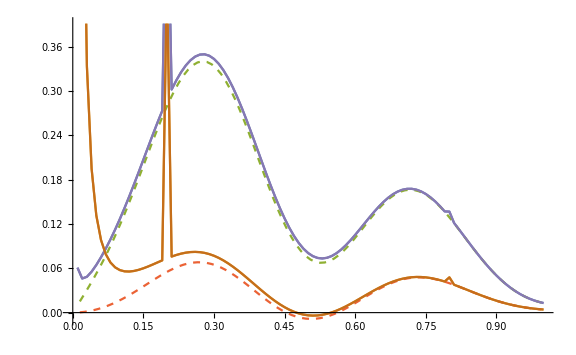

```mathematica
ListLinePlot[{f1pcl1[[1,;;,2,{1,3}]],f1pcl2[[1,;;,2,{1,3}]],f1cl1[[;;,2,{1,3}]],f1cl2[[;;,2,{1,3}]],f1pcl1n70[[1,;;,2,{1,3}]],f1pcl2n70[[1,;;,2,{1,3}]]}(*,PlotMarkers->{"◆", 8}*),ImageSize->Large,PlotStyle->{Default,Default,Dashed,Dashed}]
```

```mathematica
f1col1=Table[{r,t,F1[50,1][r,t]},{r,0.015`64,1.`64,0.01`64},{t,1.71`64,1.71`64,.2`64}];
f1col2=Table[{r,t,F1[50,2][r,t]},{r,0.015`64,1.`64,0.01`64},{t,1.71`64,1.71`64,.2`64}];
```

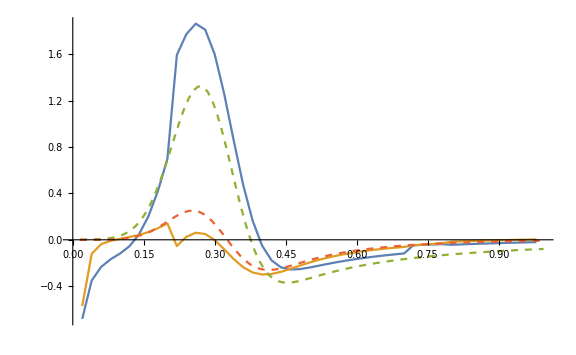

```mathematica
ListLinePlot[{f1pcol1n50[[1,;;,1,{1,3}]],f1pcol2n50[[1,;;,1,{1,3}]],f1col1[[;;,1,{1,3}]],f1col2[[;;,1,{1,3}]](*,f1pcol1n70[[1,;;,1,{1,3}]],f1pcol2n70[[1,;;,1,{1,3}]]*)}(*,PlotMarkers->{"◆", 8}*),ImageSize->Large,PlotStyle->{Default,Default,Dashed,Dashed},PlotRange->All]
```

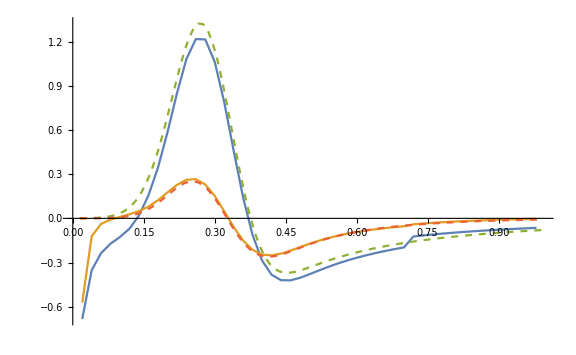

```mathematica
f2col1=Table[{r,t,80F2[50,1][r,t]},{r,1.015`64,4.`64,0.05`64},{t,0,0,.2`64}];
f2col2=Table[{r,t,80F2[50,2][r,t]},{r,1.015`64,4.`64,0.05`64},{t,0,0,.2`64}];
```

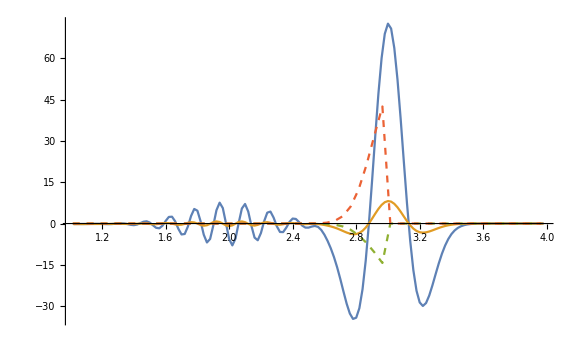

```mathematica
ListLinePlot[{f2pcol1n50[[1,;;,1,{1,3}]],f2pcol2n50[[1,;;,1,{1,3}]],f2col1[[;;,1,{1,3}]],f2col2[[;;,1,{1,3}]]}(*,PlotMarkers->{"◆", 8}*),ImageSize->Large,PlotStyle->{Default,Default,Dashed,Dashed},PlotRange->All]
```

```mathematica
testrt=Table[{r,Re[F1p[60,1][r,t]]},{r,.1`64,1.`64,.1`64},{t,.5`64,.5`64,.2`64}]
```

{{{0.1,0.0016086089620352486971485116961827384487909050696044952272}},{{0.2,0.0027324119555105918083800744045333937393606746519649399321}},{{0.3,-0.001233404163494423209327586439349914088014476503099901485}},{{0.4,-0.0086505464047614970737885465916605141895120764254063704962}},{{0.5,-0.02653429351375657750667056717428754815723781134815254814748}},{{0.6,-0.0050403172861250711242675940496836962641182869943939794684}},{{0.7,0.35198757491059493200373117459651820630756052684784541645551}},{{0.8,0.3102860263682213628039229843057363298447703381450452955251}},{{0.9,-0.07228722830704077216337439204698011342936382500995399926784}}}

```mathematica
Dimensions[testrt]
```

{9,1,2}

```mathematica
checkrt=Table[{r,Re[F1[60,1][r,t]]},{r,.1`64,1.`64,.01`64},{t,.5`64,.5`64,.2`64}];
```

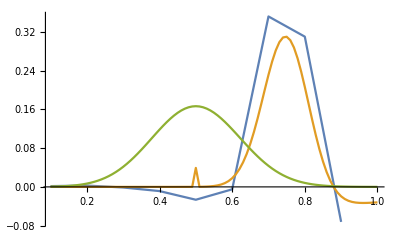

```mathematica
ListLinePlot[{testrt[[;;,1,;;]],checkrt[[;;,1,;;]],frs},PlotRange->All]
```

```mathematica
testrt[[;;,1,2]]-frs[[;;,2]]
```

{-3.73886×10^-13,-5.5718×10^-9,-4.55393×10^-6,-0.000246109,-0.000926849,-0.000248965,-4.84526×10^-6,-6.92656×10^-9,-7.36586×10^-13}

```mathematica
%1238//Dimensions
```

{8,2,2}

```mathematica
frs=Table[{r,1/6 fr},{r,.1,1.,.01}];
```

```mathematica
f1=Table[{r,2F1[70,1][r,0]},{r,.1`64,.9`64,.1`64}]
```

{{0.1,5.6769447682106097412577225969498204489261909773038×10^-10+0. ⅈ},{0.2,7.23709458964707622731894123665324055983060224647705414×10^-6+0. ⅈ},{0.3,0.005349107129063767556275379161792095787979422268721635200422+0. ⅈ},{0.4,0.27167642051595129113818264957202221760487500571679307472018+0. ⅈ},{0.5,1.00000000000000002579679888837803113336688394631042024886855+0. ⅈ},{0.6,0.273165226060575262496638986094036246588799705389071928694967+0. ⅈ},{0.7,0.005608187118926609399737054746445760140378391323022342439102+0. ⅈ},{0.8,8.719084005888837418595678747912302439978189348732952718×10^-6+0. ⅈ}}

```mathematica
{rp/cc2-R/cc2+r/cc1-R/cc1+t,
rp/cc2-R/cc2+r/cc1+R/cc1+t,
-rp/cc2+R/cc2-r/cc1+R/cc1-t,
-rp/cc2+R/cc2-r/cc1-R/cc1-t}/.{cc1->c1,cc2->c2,R->1,t->4/10,r->5./10}//TableForm
```

-0.6+rp/2
1.4+rp/2
0.6-rp/2
-1.4-rp/2

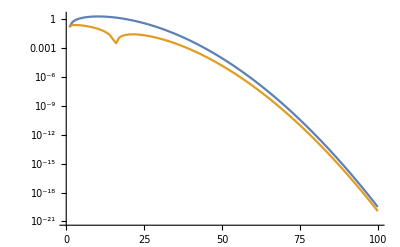

```mathematica
ListLogPlot[Transpose[Table[{{n,n},Abs[ReIm[a0[n,1]]]},{n,100}],{2,3,1}],PlotRange->All,Joined->True]
```

```mathematica
Do[
TH1[l,0]=NIntegrate[√((2l+1)/(4π))D[(fθ), θ]((l+1)LegendreP[l+1,0,Cos[θ]]-(l+1)Cos[θ]LegendreP[l,0,Cos[θ]]),{θ,0,π},AccuracyGoal->Automatic];
TH2[l,0]=NIntegrate[√((2l+1)/(4π))fθ/Sin[θ] LegendreP[l,0,Cos[θ]],{θ,0,π},AccuracyGoal->Automatic];

Do[
TH1[l,m]=NIntegrate[√((2l+1)/(4π))√(((l-m)!)/((l+m)!))D[(fθ), θ]((l+1-m)LegendreP[l+1,m,Cos[θ]]-(l+1)Cos[θ]LegendreP[l,m,Cos[θ]]),{θ,0,π},AccuracyGoal->Automatic];
TH2[l,m]=NIntegrate[√((2l+1)/(4π))√(((l-m)!)/((l+m)!))fθ/Sin[θ] LegendreP[l,m,Cos[θ]],{θ,0,π},AccuracyGoal->Automatic];
TH1[l,-m]=(-1)^m TH1[l,m];
TH2[l,-m]=(-1)^m TH2[l,m];
,{m,1,l}]
,{l,lmax}]//Timing
```

{0.21875,Null}

```mathematica
PH1[0]=NIntegrate[fϕ,{ϕ,0,2π}];
PH2[0]=0;
Do[
PH1[m]=NIntegrate[fϕ Exp[-ⅈ m ϕ],{ϕ,0,2π},AccuracyGoal->Automatic];
PH2[m]=NIntegrate[-ⅈ m D[(fϕ), ϕ]Exp[-ⅈ m ϕ],{ϕ,0,2π},AccuracyGoal->Automatic];

PH1[-m]=Conjugate[PH1[m]];
PH2[-m]=Conjugate[PH2[m]];
,{m,1,lmax}];//Timing
```

{0.015625,Null}

```mathematica
Do[
G[l][θ_,ϕ_]=Sum[(TH1[l,m]PH1[m]+TH2[l,m]PH2[m])√((2l+1)/(4π))√(((l-m)!)/((l+m)!))Exp[I m ϕ]/Sin[θ]((l+1-m)LegendreP[l+1,m,Cos[θ]]-(l+1)Cos[θ]LegendreP[l,m,Cos[θ]]),{m,-l,l}];
,{l,lmax}];
```

```mathematica
Do[
H[l][θ_,ϕ_]=Sum[(TH1[l,m]PH1[m]+TH2[l,m]PH2[m])√((2l+1)/(4π))√(((l-m)!)/((l+m)!))(-I m)Exp[I m ϕ]/Sin[θ] LegendreP[l,m,Cos[θ]],{m,-l,l}];
,{l,lmax}];
```

```mathematica
Uϕ1l[n_,l_][r_,θ_,ϕ_,t_]:=F1[n,l][r,t]G[l][θ,ϕ];
Uθ1l[n_,l_][r_,θ_,ϕ_,t_]:=F1[n,l][r,t]H[l][θ,ϕ];
Uϕ2l[n_,l_][r_,θ_,ϕ_,t_]:=F2[n,l][r,t]G[l][θ,ϕ];
Uθ2l[n_,l_][r_,θ_,ϕ_,t_]:=F2[n,l][r,t]H[l][θ,ϕ];
```

## Compare against Initial Condition

```mathematica
prerror=Table[{r,
Piecewise[{{l(l+1)Re[F1[n,l][r,t]](*-fr *),r≤Rs},{l(l+1)Re[F2[n,l][r,t]](*-fr*) ,r>Rs}}]},
{l,1},{n,{50}},{t,0,.5`64,.1`64},{r,(*rlog*).01`64,3.5`64,.05`64}];
```

```mathematica
ListPlot[prerror[[1,1,;;,11;;70]],PlotRange->{All,All(*{1*^-20,2*^1}*)},Joined->True,Frame->True,FrameLabel->{"r / R_s","Amplitude"},PlotLabel->"ℓ = 1"(*,PlotMarkers->{"■",8}*)]
```

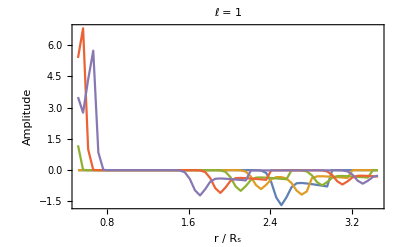

```mathematica
nknlist={50,70,100};
```

```mathematica
rkn=Function[x,1.`64*10^(x/10)]/@Range[-30,-10];
```

```mathematica
knee=Table[{r,Abs[l(l+1)F1[n,l][r,0] ]},
{l,2},{n,nknlist},{r,rkn(*.001`64,.01`64,.0005`64*)}];
```

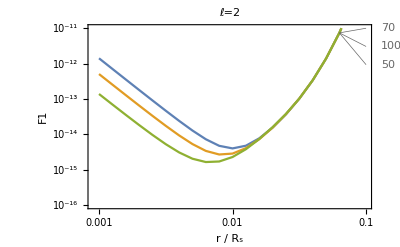

```mathematica
ListLogLogPlot[knee[[2]],PlotRange->{1*^-16,1*^-11},Joined->True,PlotLabels->nknlist,Frame->True,FrameLabel->{"r / R_s","F1"},PlotLabel->"ℓ=2"]
```

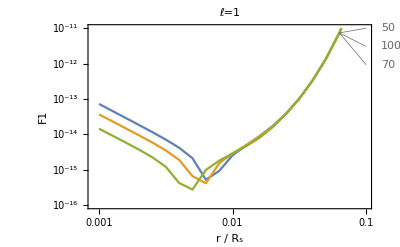

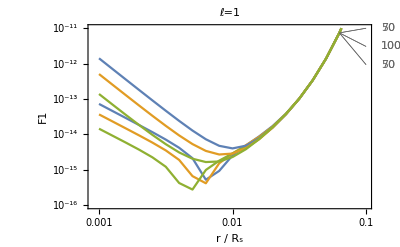

```mathematica
Show[%630,%631]
```

```mathematica
nlist={(*10,20,30,40,*)50(*,60,70,80,90,100*)};
```

```mathematica
rlog=Function[x,1.`64*10^(x/8)]/@Range[-48,6];
```

```mathematica
F2[50,1][3`64,0]
```

-0.015394123016904188074931830789164270575609832533234296917449+0. ⅈ

```mathematica
ncon=Table[{r,
Piecewise[{{Abs[l(l+1)Re[F1[n,l][r,0]]-fr ],r≤Rs},{Abs[l(l+1)Re[F2[n,l][r,0]]-fr] ,r>Rs}}]},
{l,1},{n,nlist},{r,(*rlog*).01`64,4.`64,.01`64}];
```

```mathematica
ListLogPlot[ncon[[;;,1,;;-102]],PlotRange->{All,All(*{1*^-20,2*^1}*)},Joined->True,(*PlotLabels->nlist,*)Frame->True,FrameLabel->{"r / R_s","Absolute Error"},PlotLabel->"ℓ = 1, 2"(*,PlotMarkers->{"■",8}*)]
```

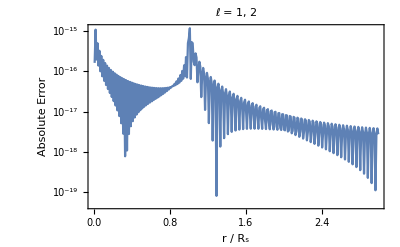

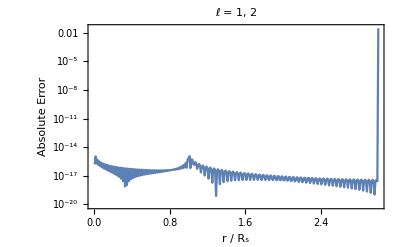

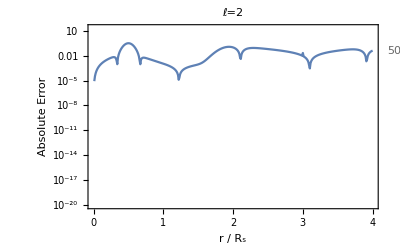

```mathematica
ListLogPlot[ncon[[2,;;,;;]],PlotRange->{All,{1*^-20,2*^1}},Joined->True,PlotLabels->nlist,Frame->True,FrameLabel->{"r / R_s","Absolute Error"},PlotLabel->"ℓ=2"]
```

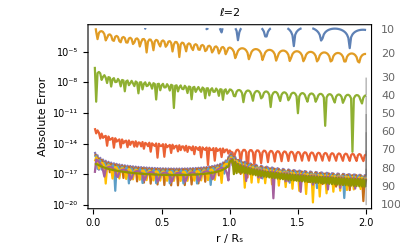

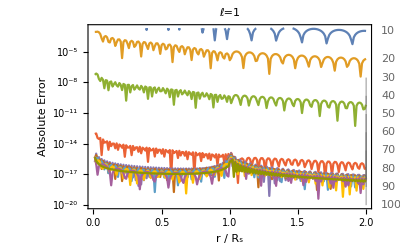

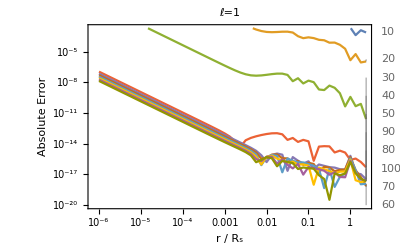

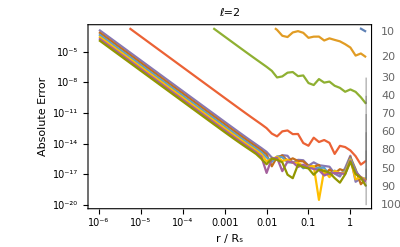

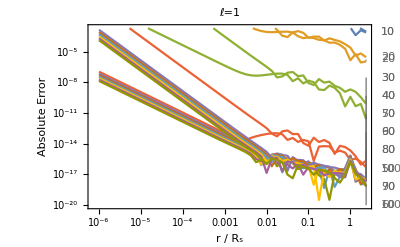

```mathematica
Show[%581,%580]
```

```mathematica
nnconv=Table[{rr(*nn*),lli(lli+1)a1[nn,lli](SphericalHankelH1[lli,(rr ww[nn,lli])/c1]((1-UnitStep[-(rr/c1+tt)])Exp[I ww[nn,lli]tt]+(1-UnitStep[-(rr/c1-tt)])Exp[-I ww[nn,lli]tt])+SphericalHankelH2[lli,(rr ww[nn,lli])/c1]((1-UnitStep[-(-(rr/c1)+tt)])Exp[I ww[nn,lli]tt]+(1-UnitStep[-(-(rr/c1)-tt)])Exp[-I ww[nn,lli]tt]))/.{(*lli->2,*)(*rr->.00001`64,*)tt->0}},{lli,2},{nn,{100(*,90,100*)}(*1,100,1*)},{rr,.01,3,.0005}];
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 2 iterations.

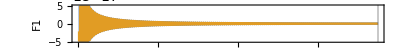

```mathematica
ListPlot[Join[nnconv[[1]],nnconv[[2]]],Joined->True,Frame->True,FrameLabel->{"r / R_s","F1"},PlotLabel->"n = 100, t = 0",PlotLabels->{"ℓ=1","ℓ=2"}(*,PlotStyle->{Default,Dashed,Default,Dashed}*),AspectRatio->1/8,ImageSize->Full,PlotRange->{-5 1*^-17,5 1*^-17}]
```

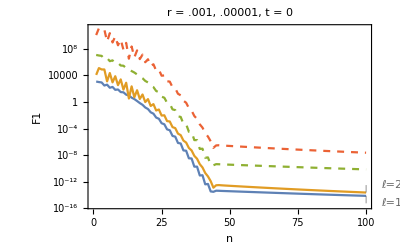

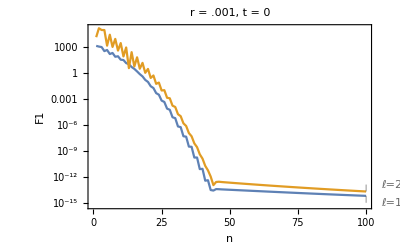

```mathematica
SetDirectory["C:\\Users\\joebr\\OneDrive\\Documents\\QPO Research\\Mathematica Plots"];
FileNames[]
Export["c2l1a2knee.png",%638,ImageResolution->200]
```

{c100comp.png,c10InPS.png,c10OnPS.png,c10OutPS.png,c10PSout.png,c10PSout.svg,c10PSstr.png,c10PSstr.svg,c10r00p5.png,c10r01p0.png,c10r01p5.png,c2EVsl40.png,c2EVsl5.png,c2F1n00100001.png,c2F1n001.png,c2l1a2Rsnconv.png,c2l1knee.png,c2l1nconv.png,c2l1nconvzoom.png,c2l1Rsnconv.png,c2l2knee.png,c2l2nconv.png,c2l2nconvzoom.png,c2l2Rsnconv.png,ComparisonByl.png,Divergl.png,Divergn.png,modesc2.gif,modesmu2.gif,NoPeak.gif,Peak.gif,Simxy_U_th.gif,Simxz.gif,SmallrConvergence.png,SmallrConv.png,smoothingCentered.gif,smoothing.gif}

c2l1a2knee.png

## Evaluation in r and t

```mathematica
(* Discretized r and t *)
Δr=.005`32;
Ri=Δr;
Rb=2.;
Rp=1.105`48;
ti=0.`48;
tf=0.`48;
Δt=.01`48;
```

```mathematica
rvs=Function[x,1.*10^x]/@Range[-5,-1]
```

{0.00001,0.0001,0.001,0.01,0.1}

```mathematica
(* Evaluate r Kernel Integrals *)
uϕe=Table[{r,Sum[Uϕ1l[n,l][r,1.1π/2,π,t],{l,lm}]},{n,{30}},{lm,1,10},{r,(*rvs*)Ri,20Δr,Δr},{t,ti,tf,Δt}];//Timing
```

{21.6563,Null}

```mathematica
With[{r=.0000000001`64},
{Uϕ1l[50,1][r,1.1π/2,π,0],
F1[50,1][r,0]}//TableForm]
```

0.224331-3.74211×10^-33 ⅈ
-4.857530709+0. ⅈ

```mathematica
Dimensions[uϕe]
```

{1,10,20,1,2}

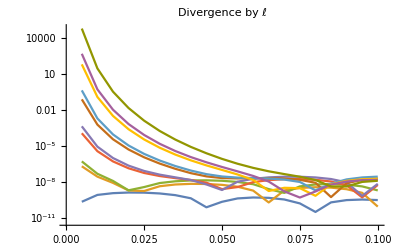

```mathematica
ListLogPlot[Abs[uϕe[[1,;;,;;,1]]](*,PlotRange->{1*^-17,1*^24}*),Joined->True(*,PlotLabels->{"10","20","30","35","40","50"}*)(*ToString/@Range[lmax]*),PlotLabel->"Divergence by ℓ"]
```

```mathematica
With[{rr=.05`32,l=1,n=40},
{l(l+1)F1[n,l][rr,0],
fr/.r->rr,
Abs[l(l+1)F1[n,l][rr,0]-fr]/fr/.r->rr}//TableForm]
```

5.565818599737377×10^-12+0. ⅈ
5.534610071701023070927722941553×10^-12
0.00563879435625032

```mathematica
convn=Table[{n,Abs[l(l+1)F1[n,l][rr,0](*-0fr*)](*/fr/.r->rr*)},{l,1,3,1},{rr,{.001`64,.005`64,.01`64,.05`64,.1`64,.15`64}},{n,20,50,1}];
```

```mathematica
grdlns=fr/.r->#&/@{.001,.005,.01,.05,.1,.15}
```

{1.43917×10^-14,2.39406×10^-14,4.49691×10^-14,5.53461×10^-12,1.27541×10^-9,1.54975×10^-7}

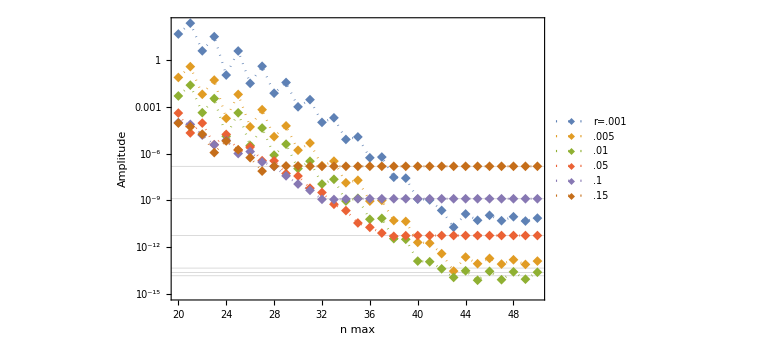

```mathematica
ampnplot3=ListLogPlot[convn[[3]],Joined->True,PlotMarkers->{"◆", 10},PlotLegends->{"r=.001",".005",".01",".05",".1",".15"},Frame->True,FrameLabel->{"n max","Amplitude"},GridLines->{{},grdlns},ImageSize->Large,PlotStyle->Dotted]
```

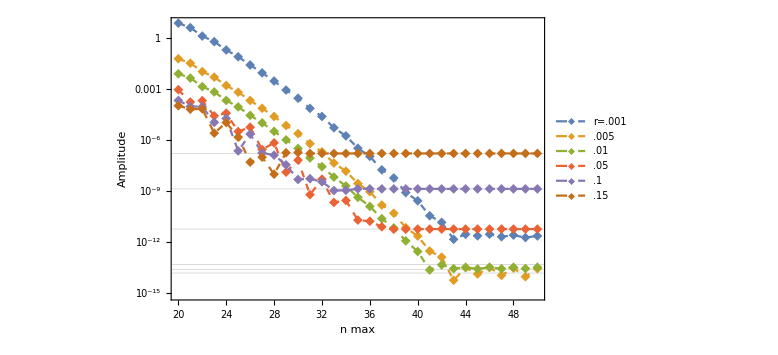

```mathematica
Show[ampnplot2]
```

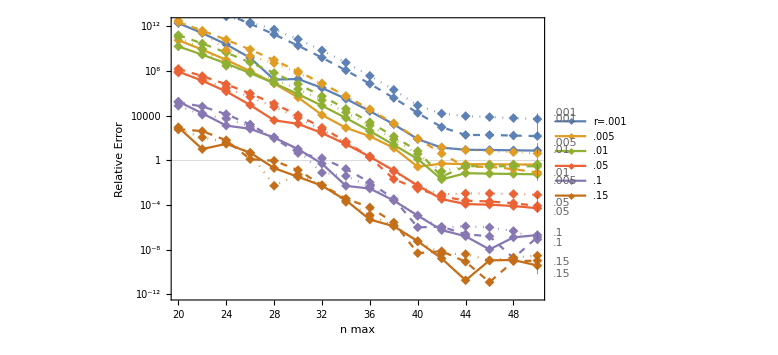

```mathematica
Show[convnplot1,convnplot2,convnplot3]
```

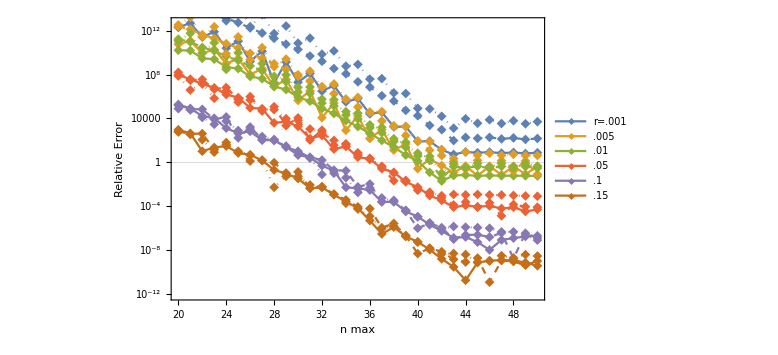

```mathematica
Show[convn64plot1,convn64plot2,convn64plot3]
```

```mathematica
Limit[A2[#,ω],ω->0]&/@{1,2,3,4,5}
```

{4/3,8/3,16/3,32/3,64/3}

```mathematica
With[{l=2,r=1},Plot3D[Abs[((x+ⅈ y)^2 SphericalHankelH1[l,r(x+ⅈ y)])/(A1[l,x+ⅈ y]A2[l,x+ⅈ y])],{x,-4,4},{y,-4,4},PlotRange->{0,5},AxesLabel->{"x","y"}]]
```

-Graphics3D-

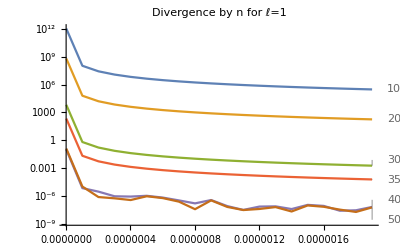

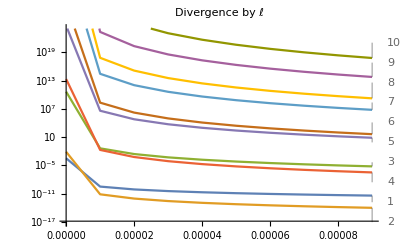

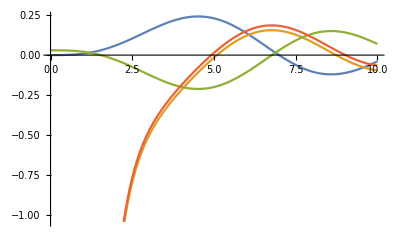

```mathematica
With[{l=3},Plot[{Re[SphericalHankelH1[l,x]],Im[SphericalHankelH1[l,x]],Re[SphericalHankelH1[l,-x]]+.03,Im[SphericalHankelH1[l,-x]]+.03},{x,0,10}]]
```

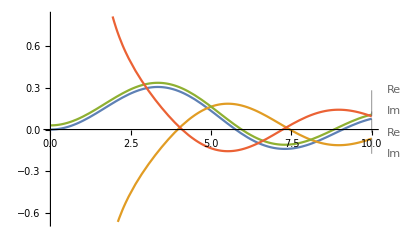

```mathematica
With[{l=2},Plot[{Re[SphericalHankelH1[l,x]],Im[SphericalHankelH1[l,x]],(-1)^l Re[SphericalHankelH1[l,-x]]+.03,(-1)^l Im[SphericalHankelH1[l,-x]]+.03},{x,0,10},PlotLabels->{"Re","Im","Re","Im"}]]
```

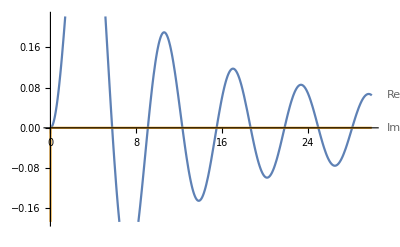

```mathematica
With[{l=2},Plot[{Re[SphericalHankelH1[l,x]+(-1)^l SphericalHankelH1[l,-x]],Im[SphericalHankelH1[l,x]+(-1)^l SphericalHankelH1[l,-x]]},{x,0,30},PlotLabels->{"Re","Im","Re","Im"}]]
```

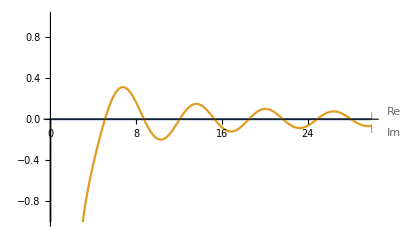

```mathematica
With[{l=3,wx=1,wy=.00001},Plot[{Re[SphericalHankelH1[l,x(wx+ⅈ wy)]+(-1)^(2l)SphericalHankelH1[l,x(-wx+ⅈ wy)]],Im[SphericalHankelH1[l,x(wx+ⅈ wy)]+(-1)^(2l)SphericalHankelH1[l,x(-wx+ⅈ wy)]]},{x,0,30},PlotLabels->{"Re","Im"},PlotRange->{-1,1}]]
```

```mathematica
Manipulate[Plot[{Re[SphericalBesselJ[l,x+ⅈ y]],Im[SphericalBesselJ[l,x+ⅈ y]]},{x,0,50}],{y,0,5,.1},{l,1,10,1,SetterBar}]
```

```mathematica
SetDirectory["C:\\Users\\joebr\\OneDrive\\Documents\\QPO Research\\Mathematica Plots"];
FileNames[]
Export[".png",%,ImageResolution->200]
```

{c100comp.png,c10PSout.png,c10PSout.svg,c10PSstr.png,c10PSstr.svg,c10r00p5.png,c10r01p0.png,c10r01p5.png,ComparisonByl.png,Divergl.png,Divergn.png,modesc2.gif,modesmu2.gif,NoPeak.gif,Peak.gif,Simxy_U_th.gif,Simxz.gif,smoothingCentered.gif,smoothing.gif}

SmallrConvergence.png

```mathematica
%385
```

-Graphics-

ListLinePlot::lpn: … is not a list of numbers or pairs of numbers.